```mathematica
(*TESTY DLA PARAMETRU*)
```

```mathematica
Test[iloscTestow_,funkcjaCelu_,ograniczenia_,typMutacji_,iloscWymiarow_,przewidywaneOptimum_]:=Module[{wyniki,osobniki,wartosci,iteracje,dane,najlepszyOsobnik,odchylenia},
wyniki={};
osobniki={};
wartosci={};
iteracje={};
odchylenia={};
Do[AppendTo[wyniki,AG[300,funkcjaCelu,20,iloscWymiarow,ograniczenia,0.2,przewidywaneOptimum,0.2,10^(-3),300,typMutacji]];Print[i],{i,1,iloscTestow}];
Do[
AppendTo[osobniki,wyniki[[i,1,1]]];
AppendTo[wartosci,wyniki[[i,1,2]]];
AppendTo[iteracje,wyniki[[i,2]]];
AppendTo[odchylenia,wyniki[[i,3]]];
,{i,1,iloscTestow}];
najlepszyOsobnik=ZnalezienieNajlepszegoOsobnika[osobniki,funkcjaCelu,iloscWymiarow,iloscTestow][[1]];
dane={najlepszyOsobnik,{N[Max[wartosci]],N[Mean[wartosci]],N[Min[wartosci]]},{N[Max[iteracje]],N[Mean[iteracje]],N[Min[iteracje]]}};
Print["Najlepsze znalezione rozwiązanie podczas testów: ",najlepszyOsobnik[[1]],", o wartosci funkcji celu: ",najlepszyOsobnik[[2]]];
Print["Maksymalna wartość funkcji celu: ",N[Max[wartosci]],", Średnia wartość funkcji celu: ", N[Mean[wartosci]], ". Minimalna wartosc funkcji celu: ", N[Min[wartosci]]];
Print["Największa ilość potrzebnych iteracji: ",N[Max[iteracje]],". Średnia ilość potrzebnych iteracji: ",N[Mean[iteracje]],". Najmniejsza ilość potrzebnych iteracji: ",N[Min[iteracje]]];
Print["Największe odchylenie w ostatniej populacji: ",N[Max[odchylenia]],". Średnie odchylenie w ostatniej populacji: ",N[Mean[odchylenia]],". Najmniejsze odchylenie w ostatniej populacji: ",N[Min[odchylenia]]];
Print[Histogram[wartosci,AxesLabel->{"Wartości funkcji"},LabelingFunction->Above]];
Print[Histogram[iteracje,AxesLabel->{"Ilość iteracji"},LabelingFunction->Above]];
Print[Histogram[odchylenia,AxesLabel->{"Odchylenia standardowe"},LabelingFunction->Above]];
Return[dane]]
```

```mathematica
TestZParametrem[iloscTestow_,funkcjaCelu_,ograniczenia_,iloscWymiarow_,przewidywaneOptimum_]:=Module[{wyniki,osobniki,wartosci,iteracje,dane},
dane={};
Do[wyniki={};
osobniki={};
wartosci={};
iteracje={};
Do[
Do[
AppendTo[wyniki,AG[100,funkcjaCelu,20,iloscWymiarow,ograniczenia,0.2,przewidywaneOptimum,j,10^(-2),100,"zParametrem"]]
,{j,0.1,1,0.1}]
,{i,1,iloscTestow}];
Do[
AppendTo[osobniki,wyniki[[i,1,1]]];
AppendTo[wartosci,wyniki[[i,1,2]]];
AppendTo[iteracje,wyniki[[i,2]]]
,{i,1,iloscTestow}];
AppendTo[dane,{j,ZnalezienieNajlepszegoOsobnika[osobniki,funkcjaCelu,2,iloscTestow][[1]],{N[Max[wartosci]],N[Mean[wartosci]],N[Min[wartosci]]},{N[Max[iteracje]],N[Mean[iteracje]],N[Min[iteracje]]}}]
,{j,1,0.1,-0.1}];
Return[dane]]
```

```mathematica
(*TESTY DLA DETERMINISTYCZNEJ KONTROLI*)
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

Najlepsze znalezione rozwiązanie podczas testów: {1.00115,1.00227,0.0350268}, o wartosci funkcji celu: 1.39309×10^-6

Maksymalna wartość funkcji celu: 0.000923372, Średnia wartość funkcji celu: 0.000469063. Minimalna wartosc funkcji celu: 1.39309×10^-6

Największa ilość potrzebnych iteracji: 181.. Średnia ilość potrzebnych iteracji: 31.5. Najmniejsza ilość potrzebnych iteracji: 7.

Największe odchylenie w ostatniej populacji: 2.52923×10^6. Średnie odchylenie w ostatniej populacji: 126473.. Najmniejsze odchylenie w ostatniej populacji: 0.00440162

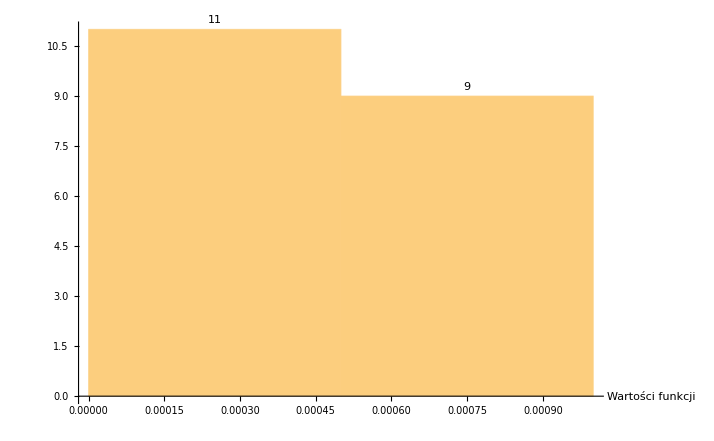

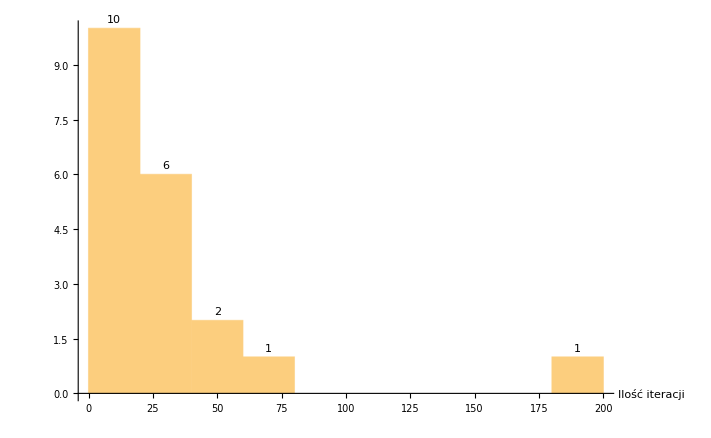

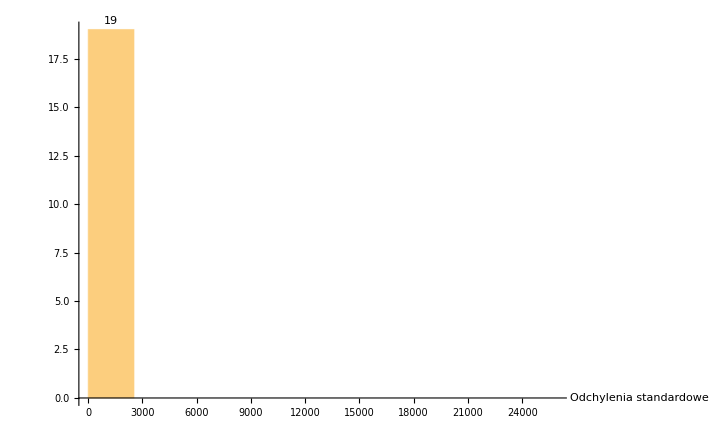

{{{1.00115,1.00227,0.0350268},1.39309×10^-6},{0.000923372,0.000469063,1.39309×10^-6},{181.,31.5,7.}}

```mathematica
l=Test[20,(1-x1)^2+100*(x2-x1^2)^2,{{-5,5},{-5,5}},"samoadaptujaca",2,0]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

Najlepsze znalezione rozwiązanie podczas testów: {1.01036,1.02113}, o wartosci funkcji celu: 0.000115917

Maksymalna wartość funkcji celu: 0.000985898, Średnia wartość funkcji celu: 0.000599322. Minimalna wartosc funkcji celu: 0.000115917

Największa ilość potrzebnych iteracji: 261.. Średnia ilość potrzebnych iteracji: 112.65. Najmniejsza ilość potrzebnych iteracji: 17.

Największe odchylenie w ostatniej populacji: 157.589. Średnie odchylenie w ostatniej populacji: 59.0105. Najmniejsze odchylenie w ostatniej populacji: 4.21104

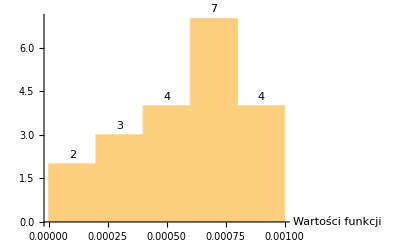

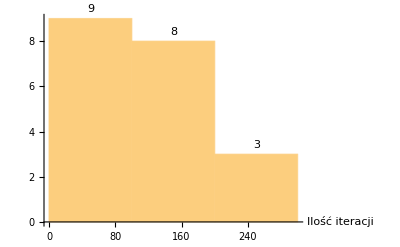

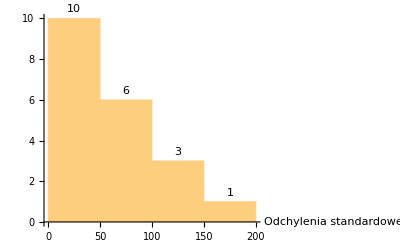

{{{1.01036,1.02113},0.000115917},{0.000985898,0.000599322,0.000115917},{261.,112.65,17.}}

```mathematica
Test[20,(1-x1)^2+100*(x2-x1^2)^2,{{-5,5},{-5,5}},"deterministyczna",2,0]
```